# Gravity Tunnel in the Earth

A novel effective function for the mass density profile inside the Earth is proposed in order to describe qualitatively and quantitatively physical aspects of the terrestrial density derived from seismic models. This was done using a decreasing potential law function dependent only on the distance to the center of the Earth and on some parameters, in such a way that central density, surface density and total mass are correctly given. This effective function was applied to gravity tunnel concepts as a test of the predictive power of the effective model, but the comparison is established with the geophysical approach predictions, in the place of real life experiments, due to the impossibility of performing this. A high correspondence between the effective model and the reference model was found.

## 1 Introduction

A gravity tunnel is a hypothetical means of transportation in which, to arrive to one point to another on the surface of the planet, it appeals to the acceleration of gravity in a tunnel connecting both points. The problem is clearly pedagogic and has been thoroughly discussed in journals of this character.  
  
    This has been made in a lot of different ways, considering the simplest case of constant density, proposed as exercise in classical mechanics  textbooks, adding rail’s friction, or considering the rotation of the Earth , and the effect of this in its geometrical form, or even in the frame of general relativity . Likewise, this has been done considering density-pressure relations based on polytrope , or in more accurate density geophysical models as the Preliminary Reference Earth Model (PREM), being this last one done numerically by Klotz , making a comparison with a constant gravity approximation; and also doing an analytical treatment using a linear, piecewise approximation which throw closer results to those of the PREM, and which get out the poorly physical situation of a constant gravity  (since this implies infinitive densities at the center of the planet).

    To geophysical, astrophysical, as well as purely physical purposes, knowing the density distribution inside of our planet is of great utility. In a first approximation and to uniquely illustrative aims, it can be taken to be constant, dividing total mass under its volume and getting     ρ=5513kg/m^3.
    
    With this one can obtain approximate values for the acceleration of gravity or moments of inertia. Nevertheless, it is clear that the density on Earth (and on any astronomical body) is far from being constant. Other models have been proposed in order to describe the density  or the acceleration  of our planet, but the most accepted model is the Preliminary Reference Earth Model, according to which the density in the interior has discontinuities between the different layers that form it: inner core, outer core, mantle and crust. Inside each region, density can be approximated with a polynomial function . This can be seen on the figure above . Notice that density increases towards the center and reaches its maximum value around 1300kg/m^3, while in the surface is almost 1020kg/m^3, which corresponds to the density of the water of the ocean.
    
     In the present work it is intended to discuss a possible approximation to this model using an effective density function more simple to express: soft, continuous and certainly not constant.  This function is contemplated as a possible replacement to the described for the Reference Model and, thus, as a simple but accurate description of Earth physical effects.
     
      The use of this function not only represents a totally different treatment compared to those previously mentioned for the treatment of the gravity tunnel, but also serves as an example to illustrate the construction and the development of an effective model. Effective models in classical mechanics and, actually in undergraduate physics, are very rare. Nonetheless its utility  in the scientific world is becoming greater and greater; hence, it is important that students at this level in a physics or engineering career get familiar with some model with a simple and fairly known physics and that doesn’t contain any complicated mathematical or computational methods. The present article accomplish all those requirements due to the simple deductions, presented in the field of Newton mechanics, and to the functions used, which are integrable  either in analytical form or with the conventional numerical methods.

    For the effective density function construction, the density profiles are first raised in section 2, were conditions over the parameters to fix are stated. Total mass and gravity are computed as consistency checks in section 3, then, speed profiles, traversal times and brachistochrone shapes are computed and compared in 4. 
    
    Finally, in , we study the acceleration along the path, in order to give a dynamic explanation of why the times are shorter for longer paths such as brachistochrone, and not for the paths of shorter distance.

To see PREM density we need to  import the data

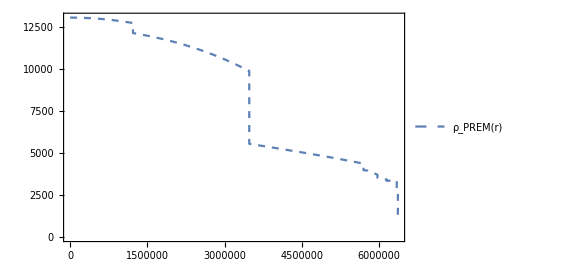

```mathematica
data=Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/prem-density.csv","Table"];
density prem=ListLinePlot[data,
PlotLegends->Placed[{"ρ_PREM(r)"},{Right,Top}],
PlotStyle->Dashed,
Frame->True]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Plots/density_prem.pdf",density prem];
```

Before continue, let’s define the value of the constants that we are going to use: Acceleration of gravity, radius of the Earth, mean density of the Earth and gravity constant:

```mathematica
g=9.8156;  (*m/s2*)  
R=6.371 10^6; (*m*) 
ρ0 = 5513 ; (*kg/m3*)
G = 6.67 10^(-11) ;(* N m2/kg^2*)
```

## 2 The Model

In order to account for a density that replaces the one in fig. above, with a continuous and soft form, but such that it reproduces the following geophysical situations

Density in the center of the Earth:

```mathematica
ρ(0)=Subscript[ρ, 0] b =13088.5
```

Density at the surface must be that of the water (1020kg/m^3):

```mathematica
ρ(r = R) = b Subscript[ρ, 0](1-c )^d = Subscript[ρ, s]
```

The third conditions is given from the total mass, we must have

```mathematica
Subscript[M, T] = 4π ∫_0^R ρ(r)r^2 ⅆr = 4π Subscript[ρ, 0] b∫_0^R (1 - c r/R)^d r^2 ⅆr
```

and such that it allows to make predictions, we have considered the following decreasing power law binomial function of three parameters:

```mathematica
ρ1(r; b, c, d)= Subscript[ρ, 0] b (1-c r/R)^d
```

being b,c,d parameters to determine. It can be written in the code as the function

```mathematica
ρ 1[r_,b_,c_,d_]:=ρ0 b Power[1-c r/R,d]
```

this density have the following forms

```mathematica
Manipulate[Plot[ρ 1[r,b,c,d],{r,0,R},PlotStyle-> RGBColor[b,c,d]],{b,0.2,4,0.2},{c,.1,1,0.1},{d,.1,1,0.1}]
```

Plot::plln: Limiting value R in {r,0,R} is not a machine-sized real number.

### 2.1 Density Function

Lets now use the conditions stated above to find the parameters b, c, d:

Density in the center

```mathematica
b = 13088.5/ρ0 ;
Print[Style["b = ",20,FontFamily->"Utopia"], Style[SetPrecision[b,15],20,FontFamily->"Utopia"]]
```

b = 2.37411572646472

Density at the surface, with the value of b above

```mathematica
(1-c)^d=0.1815/2.37325 = 0.0779309
```

The integral for the third conditions, done with Mathematica gives the analytical expression

```mathematica
Clear[b,R]
 Integrate[b*x^2*(1-c*(x/R))^d,{x,0,R}]
```

ConditionalExpression[(b (2+(1-c)^d (-1+c) (2+c (1+d) (2+c (2+d)))) R^3)/(c^3 (1+d) (2+d) (3+d)), Re[c]≤1||c∉ℝ]

so we can express the third condition as:

```mathematica
3 b [ 2 -  (1-c)^(d+1)(2+2c(1+d)+c^2(2+3d + d^2))]=  c^3(6 + 11d + 6 d^2+ d^3)
```

To solve the system of equations, this would be the code on Mathematica to solve the system, but it takes too long

```mathematica
Remove[x,y];
NSolve[{(1-x)^y==0.0763,7.1197(2-(1-x)^(y+1)*(2+2*x*(1+y)+x^2*(2+3*y+x^2)))/(x^3*(6+11*y+6*y^2+y^3))==1},{x,y}]
```

On the other hand, the next code on Python finds the answer in a few seconds:

from scipy.optimize import root

def equations(p):
	x, y  = p
	eq1 = (1-x)**y - 0.0779310081369141
	eq2 = 7.12235*(2 - (1 - x)**(y + 1)*(2 + 2*x*(1 + y) + x**2*(2 + 3*y + y**2))) / (x**3*(6 + 11*y + 6*y**2 + y**3)) - 1
	return ( eq1 , eq2 )
	
sol =  root(equations, (0.1, 0.1), method='lm', jac=None, tol=None, callback=None, options={'col_deriv': 0, 'xtol': 1.49012e-08, 'ftol': 1.49012e-08, 'gtol': 0.0, 'maxiter': 0, 'eps': 0.0, 'factor': 100, 'diag': None})


x = sol.x[0]
y = sol.x[1]

#print(equations((x, y)))
print('x = ', x)
print('y = ', y)

x = 0.98695
y = 0.588137

For simplicity, the density function to work from here on is then

```mathematica
b = 2.37411572646472;
c = 0.986950462357128;
d = 0.5881369116467612;
ρ[r_]:=ρ 1[r,b,c,d]
```

Plotting with this result gives

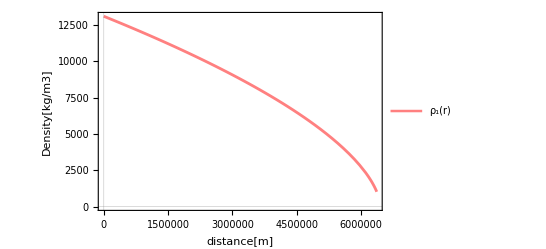

```mathematica
EffctiveFunction=Plot[{ρ[x]},{x,0,R},
PlotLegends->Placed[{"ρ_1(r)"},{Right,Top}],
PlotStyle->{Thickness[0.005],Pink},
Frame->True,
FrameLabel->{{"Density[kg/m3]",None},{"distance[m]",None}},
PlotTheme->"Scientific"]
```

To compare, we can plot them together

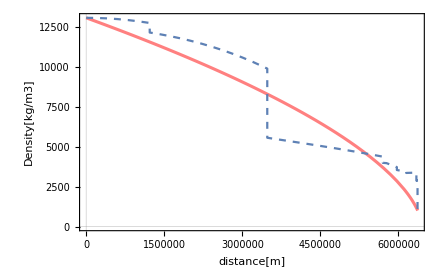

```mathematica
densities = Show[EffctiveFunction,density prem]
```

we see that actually the proposed functions fit between the data.

### 2.2 Numerical Checks

In this section, we want to use the effective density function found to check if the numerical computation of some quantities is correct, giving us a first clue of the correctness of the method elaborated.

#### Densities

The test of the first two conditions is trivial and it’s just the minimum requirement. With all the digits we have checked that the condition values are returned.

In the surface we find:

```mathematica
Print[Style["ρ(R) = ",20,FontFamily->"Utopia"],Style[ ρ[R],20,FontFamily->"Utopia"], Style[" kg/m^3 ",20,Italic,FontFamily->"Utopia"]]
```

ρ(R) = 1020. kg/m^3

In the center

```mathematica
Print[Style["ρ(0) = ",20,FontFamily->"Utopia"],Style[ ρ[0],20,FontFamily->"Utopia"], Style[" kg/m^3 ",20,Italic,FontFamily->"Utopia"]]
```

ρ(0) = 13088.5 kg/m^3

#### Masses

Let’s consider now the integration of the density to find the mass, which is less immediate. With any integration algorithm, it can be seen that the following integral
Now, we want to determine the mass as a function of the radius. At r=R we would like to have M(R)=M~ 6 x10^25 kg ,

```mathematica
M[r_]:= 4 π  NIntegrate[ρ[x] x^2,{x,0,r}]
```

the output at the radius is

```mathematica
Print[Style["M_T = ",20,FontFamily->"Utopia" ],Style[M[R],20,FontFamily->"Utopia"], Style[" kg",20,Italic,FontFamily->"Utopia"]]
```

M_T = 5.97172×10^24 kg

the expected one.  To see the behaviour at any other point let’s plot this functions

```mathematica
Masses = Plot[{M[r]},{r,0,R},
PlotStyle->{{Thickness[0.008],Pink}},
Frame->True,
FrameLabel->{{"M(r) [kg]",None},{"r [m]",None}}]
```

-Graphics-

#### Gravity

The acceleration of gravity in the surface is another physical constant that must be appropriately given by our effective model. This is, however, not a prediction. Thanks to Newton’s shell theorem, total mass is what gives gravity its constant value on the surface, regardless of the distribution of mass. This fact can also be seen in the mathematical expression derivable from Gauss law (the integrals are the same):

```mathematica
a(r) = (4π G)/r^2∫_0^r ρ(r')r'^2 ⅆr'
```

The interest we have in the form of the acceleration, not only in the surface but in the inside as well, is that, to perform the predictions of the model within the context of the gravity tunnel, we will need this as a function of the radius. Furthermore, there are two ways to address this and some of the next computations. One is integrating by brute force, as we did with the expression of M_T.

```mathematica
Clear[b,c,d,R]
Integrate[x^2*(1-c*(x/R))^d,{x,0,r}]
```

ConditionalExpression[(2 R^3+(1-(c r)/R)^d (c r-R) (c^2 (1+d) (2+d) r^2+2 c (1+d) r R+2 R^2))/(c^3 (1+d) (2+d) (3+d)), ]

Now, let’s define the function as

```mathematica
a analytic [r_]:= 3 g b (2 R^2-(1-c r/R)^(d+1)(c^2(1+d)(2+d)r^2 + 2c(1+d)r R + 2 R^2))/(c^3r^2(6 + 11d + 6 d^2+ d^3))
```

At the  radius the gravity is

```mathematica
Print[Style["g_analytic = ",20,FontFamily->"Utopia"],Style[a analytic[R],20,FontFamily->"Utopia"], Style[" m/s^2",20,Italic,FontFamily->"Utopia"]]
```

g_analytic = 9.8156 m/s^2

As it should be. The other is re-writing the density using Newton’s binomial theorem

```mathematica
a (r) = (4π G)/r^2 Subscript[ρ, 0] b∫_0^r (1- c r'/R)^d r'^2 ⅆr' = (4π G)/r^2 (3M)/(4π R^3)∑_(n=0)^∞ ({{d}, {n}})(-c)^n/R^n∫_0^r r^(n+2)ⅆr
	= 3 g b  ∑_(n=0)^∞ ({{d}, {n}})(-c)^n/(n+3) (r/R)^(n+1)
```

in the code

```mathematica
a[r_]:=3 b g Sum[QBinomial[d,n,1] (-c)^n(r/R)^(n+1)/(n+3),{n,0,Infinity}]
```

at the surface we have

```mathematica
Print[Style["g_Binom = ",20,FontFamily->"Utopia"],Style[a[R],20,FontFamily->"Utopia"], Style[" m/s^2",20,Italic,FontFamily->"Utopia"]]
```

g_Binom = 9.8156 m/s^2

which is a little above the expected value. 
We can both functions in the hole range by making plots

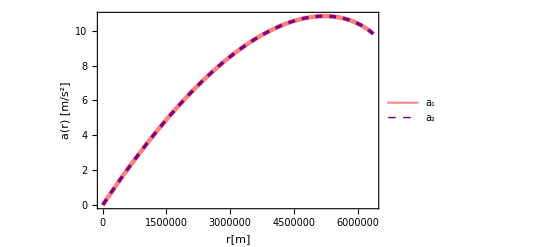

```mathematica
AccelerationFunctions=Plot[{a analytic[r],a[r]},{r,0,R},
PlotLegends->Placed[{"a_1","a_2"},{Right,Bottom}],
PlotStyle->{{Thickness[0.008],Pink},{Purple,Thickness[0.006],Dashed}},
Frame->True,
FrameLabel->{{"a(r) [m/s^2]",None},{"r[m]",None}}]
```

We see now that they are indeed the same. Now, lets import the data from PREM and plot together the founded profiles along with this one:

```mathematica
gravity prem = Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/gravity_prem.csv","Table"];
g prem=Interpolation[gravity prem,InterpolationOrder->5];
gravity prem ad = Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/prem-grav-ad.csv","Table"];
g prem ad=Interpolation[gravity prem ad,InterpolationOrder->5];
```

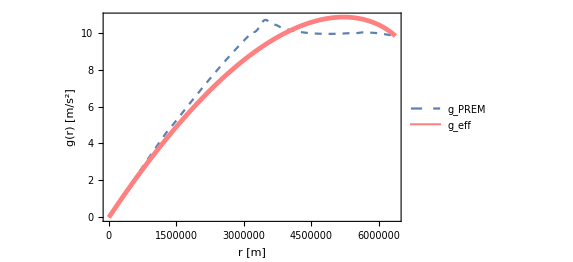

```mathematica
accelerations = Plot[{g prem[r],a[r]},{r,0,R},
PlotLegends->Placed[{"g_PREM","g_eff"},{Right,Bottom}],
PlotStyle->{Dashed,{Thickness[0.008],Pink}},
Frame->True,
FrameLabel->{{"g(r) [m/s^2]",None},{"r [m]",None}}]
```

## 4. Numerical Predictions

With the confidence on our effective density function gained above, and with the help of some physical quantities already covered, we can test the prediction power of the model . Keep in mind that, in contrast with effective model in real world, our predictions can not be tested experimentally, so we rely on the same quantities computed directly from PREM . In the next subsections we use both and compare the results .

### 4.1 Velocity Profiles

Once the mass distribution within the physical sphere to be considered is known, the speed followed by a test particle while inside it can be found from energy considerations as

```mathematica
v(r)=√(8π G ∫_r^R ∫_0^y ρ(x)x^2 ⅆx 1/y^2 ⅆy)
```

or in terms of the integral of the acceleration.  For the PREM profile, we have

```mathematica
vprem[r_?NumberQ] :=Sqrt[2*NIntegrate[g prem[x],{x,r,R}]]
vprem ad[r_?NumberQ] := Sqrt[2/3*NIntegrate[ g prem ad[x], {x, r, 1}]]
```

For the case of the effective density function, this will be the direct integration of the analytical acceleration

```mathematica
v analytic [r_]:= Sqrt[8 Pi G ρ0  NIntegrate[ b Power[1-c x /R,d]  x^2 /y^2,{y,r,R},{x,0,y}]]
```

while this is an still analytical expression using the binomial theorem expression:

```mathematica
v ad[r_]:=Sqrt[2 b Sum[QBinomial[d,k,1]*(-c)^k  (1 - r^(k+2))/((k+2)(k+3)),{k,0,Infinity}]]
v[r_]:=Sqrt[8 Pi G ρ0 R^2]Sqrt[ b Sum[QBinomial[d,k,1]*(-c)^k  (1 - r^(k+2))/((k+2)(k+3)),{k,0,Infinity}]]
```

We can see that they exactly the same and very close to the value predicted by PREM distribution

```mathematica
Print[Style["v_PREM (0)= ", 20,FontFamily->"Utopia"],Style[vprem[0],20,FontFamily->"Utopia"],Style[" m/s", 20, Italic,FontFamily->"Utopia"]," , ", 
Style["v_analytic (0)= ", 20,FontFamily->"Utopia"],Style[v analytic[0],20,FontFamily->"Utopia"],Style[" m/s", 20, Italic,FontFamily->"Utopia"]," , ",
Style["v_Binom (0)= ", 20,FontFamily->"Utopia"],Style[v[0],20,FontFamily->"Utopia"],Style[" m/s", 20, Italic,FontFamily->"Utopia"]]
```

v_PREM (0)= 9914.72 m/s , v_analytic (0)= 9839.49 m/s , v_Binom (0)= 9839.49 m/s

This represents a percentual error of

```mathematica
Print[Style["Error = ",20,FontFamily->"Utopia"],Style[(vprem[0]-v[0])/vprem[0]*100,20,FontFamily->"Utopia"],Style["%",20,FontFamily->"Utopia"]]
```

Error = 0.758851%

In the hole range, the distribution of velocities looks as

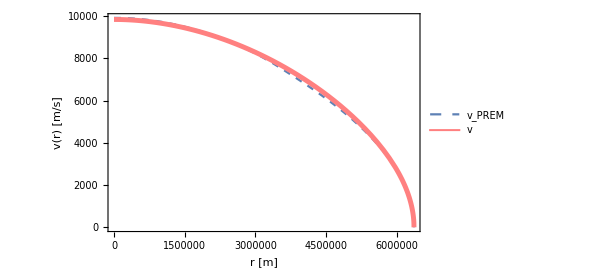

```mathematica
velocities = Plot[{vprem[x],v analytic[x]},{x,0,R},
PlotLegends->Placed[{"v_PREM","v"},{Right,Top}],
PlotStyle->{{ColorData[97][1],Dashed},{Thickness[0.008],Pink}},
Frame->True,
FrameLabel->{{"v(r) [m/s]",None},{"r [m]",None}}]
```

### 4.2 Times for the Chord Path

We have arrived to the most important part of this work, the prediction of the traversal time of the train through the chord path. In the case between antipodes, the times are given by

```mathematica
T= 2∫_0^R 1/(v(r))ⅆr.
```

in a more general chord path, characterized by a parameter d (distance from the polar axis), they are

```mathematica
T(d)= 2∫_d^R r/(v(r))1/(√(r^2-d^2))ⅆr.
```

With the velocity profiles founded above, we can define three functions for computing times; one for PREM case and two for the effective density function. The reason for having taken all this time the two methods is that analytic  functions were faster to plot above, but the integration of binomial case in this case results better, so we will define them but keep from here on, only the second case

```mathematica
Tprem[d_]:= NIntegrate[x/(vprem[x]*Sqrt[x^2 - d^2 ]),{x,d,R}]
Tprem ad[d_]:= NIntegrate[x/(vprem ad[x]*Sqrt[x^2 - d^2 ]),{x,d,1}]
T1[d_]:= NIntegrate[x/(v analytic[x]*Sqrt[x^2 - d^2 ]),{x,d,R}]
T ad[d_]:= NIntegrate[x/(v ad[x]*Sqrt[x^2 - d^2 ]),{x,d,1}]
T[d_]:= R NIntegrate[x/(v[x]*Sqrt[x^2 - d^2 ]),{x,d,1}]
```

Now, we can compute the output of this functions in minutes:

```mathematica
Print[ Style["T_PREM =",20,FontFamily->"Utopia"],Style[Tprem[0]/30,20,FontFamily->"Utopia"],Style[" min",20, Italic,FontFamily->"Utopia"],
"  ,  ",Style["T_Eff =",20,FontFamily->"Utopia"],Style[T[0]/30,20,FontFamily->"Utopia"],Style[" min",20, Italic,FontFamily->"Utopia"]]
```

T_PREM =38.1878 min  ,  T_Eff =37.7661 min

this means an error of

```mathematica
Print[ Style["Error = ",20,FontFamily->"Utopia"], Style[(Tprem[0]-T[0])/Tprem[0]*100,20,FontFamily->"Utopia"], Style[" %",20,FontFamily->"Utopia"]]
```

Error = 1.1043 %

But, again, the best way to compare the results is with a plot

```mathematica
ListTimesPrem=Table[{d,Tprem ad[d]*Sqrt[1/3* R/g]/30},{d,0,0.95,0.02}];
ListTimesEff=Table[{x,T ad[x]*Sqrt[1/3* R/g]/30},{x,0.,0.95,0.02}];
```

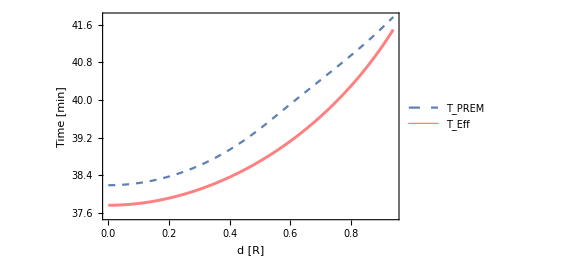

```mathematica
chordtimes = ListLinePlot[{ListTimesPrem, ListTimesEff},
PlotLegends->Placed[{"T_PREM","T_Eff"},{Left,Top}],
PlotStyle->{{ColorData[97][1],Dashed},{Pink,Thickness[0.005]}},
Frame->True,
FrameLabel->{{"Time [min]",None},{"d [R]",None}}]
```

### 4.3 Brachistochrone Path

#### Shapes of the brachistochrone

The other important part of this work is the time for the path of fastest descent and its shape. To find it we will need to perform the following integration of the trajectory:

```mathematica
θ(r) = ∫_d^r I(x,d)ⅆx
```

with the integrand

```mathematica
I(r,d)=[r^4/d^2((v(d))/(v(r)))^2- r^2]^(-1/2)
```

The next is the code to define auxiliary functions for the integration,

```mathematica
I1[x_,d_]:=1/(Sqrt[x^4/d^2 *(v ad[d]/v ad[x])^2-x^2] )
I prem[x_,d_]:=1/(Sqrt[x^4/d^2 *(vprem ad[d]/vprem ad[x])^2-x^2] )
```

With them we can proceed to do the integration in a valid range

```mathematica
θ [r_?NumericQ,d_?NumericQ]:=If[r>d,NIntegrate[I1[x,d],{x,d,r}],0.0]
θ prem [r_?NumericQ,d_?NumericQ]:=Piecewise[{{0.0, r≤ d},{NIntegrate[I prem[x,d],{x,d,r}],r>d}}]
```

In order to plot the trajectories and visualise the motion in a better way, we should make a polar plot. As this is not so immediate, even in Mathematica, we have to make some lists with the data points, which is what the next cell does

```mathematica
Step = 0.02;
Theta3=Table[{θ[i,0.3],i},{i,0.3,1,Step}];
Theta3 minus=Table[{- θ[i,0.3],i},{i,0.3,1,Step}];
Theta6=Table[{θ[i,0.6],i},{i,0.6,1,Step}];
Theta6 minus=Table[{- θ[i,0.6],i},{i,0.6,1,Step}];
ThetaPrem3=Table[{θ prem[i,0.3],i},{i,0.3,1,Step}];
ThetaPrem3 minus=Table[{- θ prem[i,0.3],i},{i,0.3,1,Step}];
ThetaPrem6=Table[{θ prem[i,0.6],i},{i,0.6,1,Step}];
ThetaPrem6 minus=Table[{- θ prem[i,0.6],i},{i,0.6,1,Step}];
```

With that data, we plot the Earth as the Black circle, and the trajectories inside it.

```mathematica
Circ = PolarPlot[1,{t,0,2 Pi},PlotStyle->{Thick,Black},Frame->True,FrameTicks->None,Axes->None];
Trajectories =ListPolarPlot[{Theta3,Theta3 minus,Theta6,Theta6 minus},Joined->True, 
PlotStyle->{{Purple,Thickness[0.006]}},Frame->True,FrameTicks->None,Axes->None,PlotLegends->Placed[{"θ_Eff(r)"},{Left,Center}]];
TrajectoriesPrem =ListPolarPlot[{ThetaPrem3,ThetaPrem3 minus,ThetaPrem6,ThetaPrem6 minus},Joined->True, 
PlotStyle->{{ColorData[97][1],Dashed}},Frame->True,FrameTicks->None,Axes->None,PlotLegends->Placed[{"θ_PREM(r)"},{Left,Center}]];
Brachistochornes = Show[Circ,Trajectories,TrajectoriesPrem ]
```

#### Times for the brachistochrone paths

In this subsection we are going to find the times for the brachistochrone paths plotted above. As this are by definition the paths of fastest descent, the times should be the minimal times. The formula to compute this times is better given by

```mathematica
Subscript[T, BRAQ]= ∫_d^r (√(1+x^2 I^2(x)))/(v(x))ⅆx
```

Where  I (r)=∂_r θ(r,d).

and  then the times for a given maximum approaching point d

```mathematica
Tbraq[d_?NumericQ]:=NIntegrate[Sqrt[1+r^2 I1[r,d]^2]/v ad[r],{r,d,1}]
Tbraq prem[d_?NumericQ]:=NIntegrate[Sqrt[1+r^2 I prem[r,d]^2]/vprem ad[r],{r,d,1}]
```

let’s check that the times taken when d=0 are the same as for the chord path

```mathematica
Print[ Style["T_PREM^BRAQ =",20],Style[Tbraq prem[0]Sqrt[1/3* R/g]/30,20],Style[" min",20, Italic],
"  ,  ",Style["T_Eff^BRAQ =",20],Style[Tbraq[0]Sqrt[1/3* R/g]/30,20],Style[" min",20, Italic]]
```

T_PREM^BRAQ =38.1875 min  ,  T_Eff^BRAQ =37.7288 min

They are almost the same, maybe it’s a question of precision, but we can trust in this results. We can see the complete dependence of the times on the position of the tunnel in the following plot

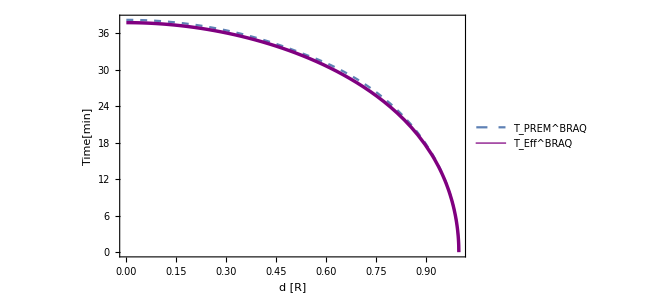

```mathematica
BraqTimes = Plot[{Tbraq prem[x]Sqrt[1/3* R/g]/30, Tbraq[x]Sqrt[1/3* R/g]/30},{ x,0,1},
PlotLegends->Placed[{"T_PREM^BRAQ","T_Eff^BRAQ"},{Left,Bottom}],
PlotStyle->{{ColorData[97][1],Dashed},{Purple,Thickness[0.005]}},
Frame->True,
FrameLabel->{{"Time[min]",None},{"d [R]",None}}]
```

### 4.4 Accelerations

In this last section, we want give a dynamical reason for the difference between chord path times and brachistochrone path times. First, define some auxiliary functions

```mathematica
dist[d_]:=Sqrt[1-(Sin[θ[1,d]])^2]
dist prem[d_]:=Sqrt[1-(Sin[θ prem[1,d]])^2]
```

with the radial accelerations and the these auxiliary functions we can define the acceleration in the direction of motion for the chord path

```mathematica
a chord[r_,d_]:=Re[a analytic[r R]/g Sqrt[r^2-(dist[d])^2]/r]
a prem chord[x_,d_]:=Re[g prem ad[x]*Sqrt[x^2-(dist prem[d])^2]/x]
```

as well as the acceleration in the direction of motion for the brachistochrone paths

```mathematica
a braq[x_,d_]:=Re[a analytic[x R]/g *Sin[θ[x, d]]]
a braq prem[x_,d_]:=Re[g prem ad[x]*Sin[θ prem[x, d]]]
```

Now, let’s plot

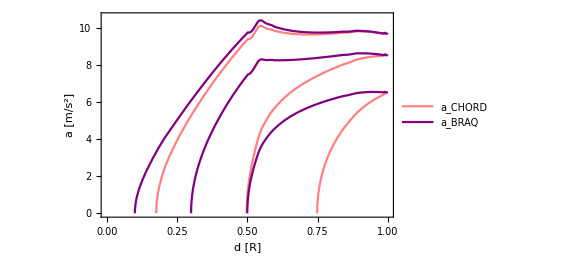

```mathematica
Accelerations chord braq =Plot[{Table[9.81*a prem chord[x,i],{i,0.1,0.5,0.2}],Table[9.81*a braq prem[x,j],{j,0.1,0.5,0.2}]},{x,0,1},
PlotRange->{0.0001,10.6},
PlotLegends->Placed[{"a_CHORD","a_BRAQ"},{Left,Top}],
PlotStyle->{Pink,Purple},
Frame->True,
FrameLabel->{{"a [m/s^2]",None},{"d [R]",None}}]
```

## 5. Geophysical Applications

### 5.1 Moment of Inertia

The moments of inertia can be defined for any object, with respect to rotation in each axis, as

```mathematica
Subscript[I, xy] = ∫_V ρ(r) (x^2+y^2)ⅆV
Subscript[I, xz] = ∫_V ρ(r) (x^2+z^2)ⅆV
Subscript[I, yz] = ∫_V ρ(r) (y^2+z^2)ⅆV
```

in the case of a sphere with density changing only around the radial direction, the three are equal, therefore, adding up we have

```mathematica
Subscript[I, xy] + Subscript[I, yz]+Subscript[I, xz] = 3 I = ∫_V ρ(r) (2 x^2 + 2 y^2 + 2 z^2 ) dV
```

hence, writing the explicit volume differential

```mathematica
I = (8 π)/3 (∫_0)^R ρ(r) r^4 dr
I = (8 π)/3 Subscript[ρ, 0] b (∫_0)^R (1 - c r/R)^d r^4 dr
```

With the effective density function found, this can be done analytically in the both ways mentioned: directly, by the method of substitution or by expansion in form of the binomial theorem (of course, numerically is also, as always, an option):

#### Analytically

The important part of the integral, namely:

```mathematica
(∫_0)^R (1 - c r/R)^d r^4 dr = R^5 (∫_0)^1 (1 - c x)^d ⅆx
```

Can be expressed as

```mathematica
Integrate[(1-c x)^d x^4,{x,0,1}]
```

ConditionalExpression[24/(c^5 (1+d) (2+d) (3+d) (4+d) (5+d))+((1-c)^(1+d) (-1/(1+d)+(4-4 c)/(2+d)-(6 (-1+c)^2)/(3+d)-(4 (-1+c)^3)/(4+d)-(-1+c)^4/(5+d)))/c^5, Re[c]≤1||c∉ℝ]

then,

```mathematica
I = (8 π)/3((3M)/(4π R^3))b  (R^5) [ % ]
```

```mathematica
I analytic = 2 M[R]R^2 b Integrate[(1-c x)^d x^4,{x,0,1}];
Print[Style["I_Analytic= ",20,FontFamily->"Utopia"],Style[ I analytic,20,FontFamily->"Utopia"],Style[" kg m^2",20,Italic,FontFamily->"Utopia"]]
```

I_Analytic= 7.72448×10^37 kg m^2

#### Using Binomial Theorem

In this case, we have

```mathematica
(∫_0)^R (1 - c r/R)^d r^4 dr = R^5 (∫_0)^1 (1 - c x)^d ⅆx = R^5 ∑_(n=0)^∞ ({{d}, {n}}) (-c)^n(∫_0)^1 x^(n+4)ⅆx = R^5 ∑_(n=0)^∞ ({{d}, {n}}) (-c)^n 1/(n+5)
```

so we get

```mathematica
I = (8 π)/3((3M)/(4π R^3))b  R^5 ∑_(n=0)^∞ ({{d}, {n}})  (-c)^n/(n+5) 
    = 2 M R^2(b∑)_(n=0)^∞ ({{d}, {n}})  (-c)^n/(n+5)
```

in this case is trivial to see that when d = 0, this reduces to the moment of inertia of a uniform sphere. Now, let’s put the parameters to get the answer

```mathematica
Ibinom = 2 M[R] R^2 b Sum[QBinomial[d,n,1](-c)^n/(n+5),{n,0,Infinity}];
Print[Style["I_BINOM= ",20,FontFamily->"Utopia"],Style[ Ibinom,20,FontFamily->"Utopia"],Style[" kg m^2",20,Italic,FontFamily->"Utopia"]]
```

I_BINOM= 7.72448×10^37 kg m^2

#### Numerically

Just to check, let’s make a last computation of the moment of inertia, directly numerically:

```mathematica
Inum = 8 Pi /3 NIntegrate[ρ[r]r^4,{r,0,R}]
Print[Style["I_Numeric= ",20,FontFamily->"Utopia"],Style[ Inum,20,FontFamily->"Utopia"],Style[" kg m^2",20,Italic,FontFamily->"Utopia"]]
```

I_Numeric= 7.72448×10^37 kg m^2

We can compare all this with the moment of inertia computed for the Earth assuming it as a uniform sphere:

```mathematica
Print[Style["I_(uniform - sphere)=2/5MR^2 = ",20,FontFamily->"Utopia"], Style[ 2/5 M[R] R^2,20,FontFamily->"Utopia"],Style[" kg m^2",20,Italic,FontFamily->"Utopia"]]
```

I_(uniform - sphere)=2/5MR^2 = 9.6956×10^37 kg m^2

### 5.2 Pressure

The relation between pressure and density (or gravity) is given by the equation of static equilibrium

```mathematica
dP/dr= -(G M(r))/r^2 ρ(r)
```

We can solve it here as a simple ODE

```mathematica
sol=NDSolve[{pressure'[r]== -   ρ[r] a analytic[r], pressure[R]==101325},pressure,{r,0.001,R}]
P[x_]:=pressure[x]/.sol[[1]];
```

{{pressure→InterpolatingFunction[…]}}

we print it’s value on the surface

```mathematica
Print[Style["P_0= ",20,FontFamily->"Utopia"],Style[P[0] ,20,FontFamily->"Utopia"],Style[" kg/ms^2",20,Italic,FontFamily->"Utopia"]]
```

P_0= 3.45935×10^11 kg/ms^2

and plot it in the whole range alongside the PREM data

```mathematica
pressure prem data = Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/1-Earth Gravity Tunnel/Numerical Data/prem_pressure.csv","Table"];
```

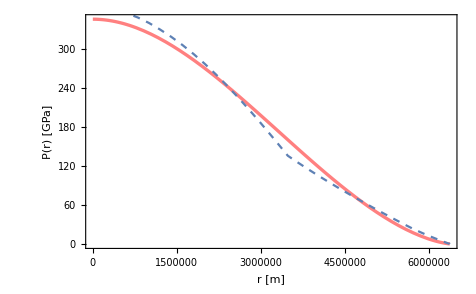

```mathematica
pressure prem=ListLinePlot[pressure prem data,
PlotLegends->Placed[{"P_PREM"},{Right,Top}],
PlotStyle->{ColorData[97][1],Dashed},
Frame->True,
FrameLabel->{{"r [m]",None},{"GP(r) [Pa]",None}}];
pressure eff=Plot[P[r] 10^-9,{r,0,R},
PlotLegends->Placed[{"P_eff"},{Right,Top}],
PlotStyle->{{Pink,Thickness[0.005]}},
Frame->True,
FrameLabel->{{"P(r) [GPa]",None},{"r [m]",None}}];
pressure plot=Show[pressure eff,pressure prem]
```

### 5.3 Temperature

First, take data from the literature

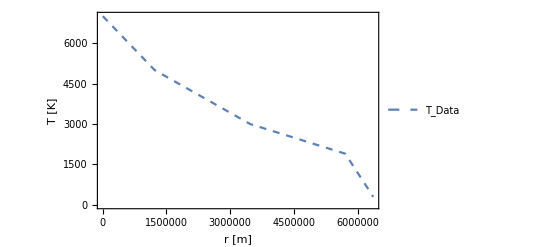

```mathematica
Temp data = {{0,7000},{1220000,5000},{3470000,3000},{5710000,1900},{6370000,300}};
Temp plot=ListLinePlot[Temp data,
PlotLegends->Placed[{"T_Data"},{Right,Top}],
PlotStyle->{ColorData[97][1],Dashed},
Frame->True,
FrameLabel->{{"T [K]",None},{"r [m]",None}}]
```

Secondly, define the effective temperature function

```mathematica
kB =1.38065 10^23 ;(*J/K*)
T1[r_,q1_,q2_]:=q1/kB P[r]/ρ[r](1-q2 r/R)
T2[r_,q1_,q2_,q3_]:=q1/kB P[r]/ρ[r](1-q2 r/R)^q3
```

```mathematica
Manipulate[{Plot[T2[x,Q1,n,ñ],{x,0,R}],Plot[T2[x,Q1,n,ñ],{x,6.3 10^6,R}]},{n,-1,1},{ñ,-1,1}]
```

We have to establish the following conditions

```mathematica
1. T(r=0) = 7000
2. T(r=R) = 300
```

the first one implies

```mathematica
Q1 = 7000 kB ρ[0]/P[0]
```

3.65659×10^19

while the second one gives

```mathematica
Q2=1-300 kB/Q1 ρ[R]/P[R]
```

-11401.8

```mathematica
T1[R,Q1,Q2]
```

300.

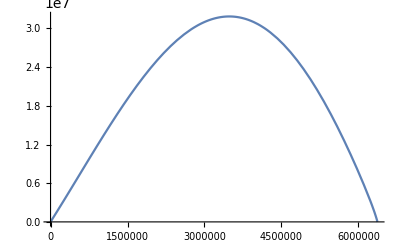

```mathematica
Plot[T1[r,Q1,Q2],{r,0,R}]
```

Consider instead just

```mathematica
T3[r_,q1_]:= q1/kB P[r]/ρ[r](1-r/R)+300
```

where

```mathematica
Q =  (7000-300) kB ρ[0]/P[0]
```

3.49988×10^19

which gives

```mathematica
T3[0,Q]
T3[R,Q]
```

7000.

300.

and

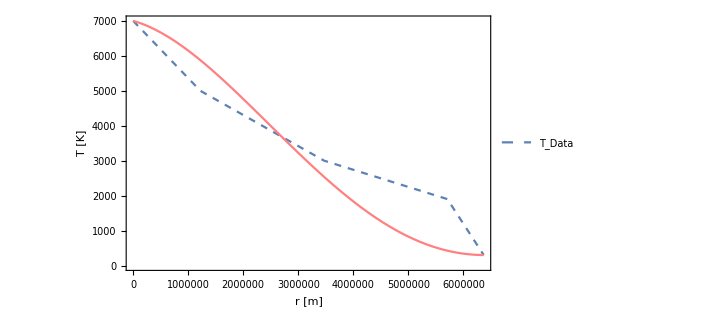

```mathematica
TempEff = Plot[T3[r,Q],{r,0,R},
PlotStyle->Pink];
Show[Temp plot,TempEff]
```